```mathematica
dist=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/3D/dist.txt","Table"];
```

```mathematica
distConf=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/3D/distConf.txt","Table"];distMarg=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/3D/distMarg.txt","Table"];
```

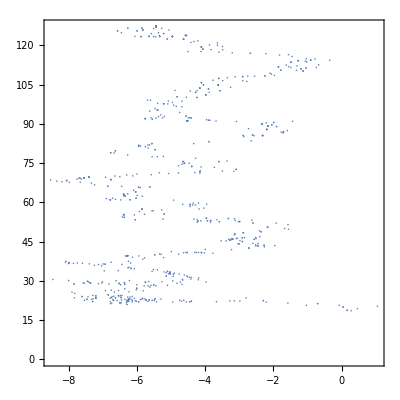

```mathematica
ListPlot[Table[{dist[[i,2]],dist[[i,3]]},{i,Length[dist]}],PlotRange->All,Frame->True,AspectRatio->1]
```

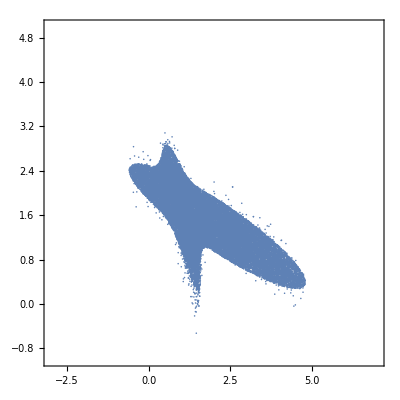

```mathematica
ListPlot[Table[{distConf[[i,2]],distConf[[i,3]]},{i,Length[distConf]}],PlotRange->{{-3,7},{-1,5}},Frame->True,AspectRatio->1]
```

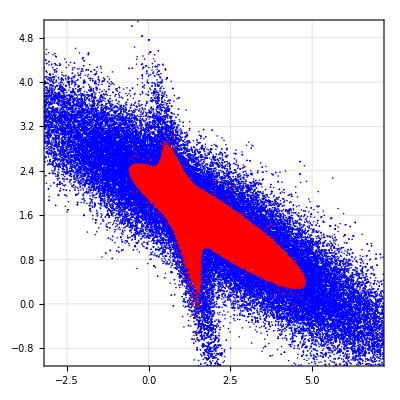

```mathematica
ListPlot[{Table[{dist[[i,2]],dist[[i,3]]},{i,Length[dist]}],Table[{distConf[[i,2]],distConf[[i,3]]},{i,Length[distConf]}]},PlotRange->{{-3,7},{-1,5}},Frame->True,AspectRatio->1,PlotStyle->{Blue,Red},GridLines->Automatic]
```

```mathematica
SigmaTot=1.;
```

```mathematica
branchWW=0.216*(1+2.2*cW);
branchZZ=0.0267*(1.+2.0*cZ);
branchGammaGamma=0.0023*(1.+5.0*cW);
```

```mathematica
fmuMeasurements={0.83,1.09,1.0,1.44,1.13,1.17};
fmuMeasurementsErr={0.21,0.22,0.29,0.37,0.24,0.27};
```

```mathematica
chi2=(SigmaTot*branchWW-fmuMeasurements[[1]])*(SigmaTot*branchWW-fmuMeasurements[[1]])/(fmuMeasurementsErr[[1]]*fmuMeasurementsErr[[1]])+(SigmaTot*branchWW-fmuMeasurements[[2]])*(SigmaTot*branchWW-fmuMeasurements[[2]])/(fmuMeasurementsErr[[2]]*fmuMeasurementsErr[[2]])+(SigmaTot*branchZZ-fmuMeasurements[[3]])*(SigmaTot*branchZZ-fmuMeasurements[[3]])/(fmuMeasurementsErr[[3]]*fmuMeasurementsErr[[3]])+(SigmaTot*branchZZ-fmuMeasurements[[4]])*(SigmaTot*branchZZ-fmuMeasurements[[4]])/(fmuMeasurementsErr[[4]]*fmuMeasurementsErr[[4]])+(SigmaTot*branchGammaGamma-fmuMeasurements[[5]])*(SigmaTot*branchGammaGamma-fmuMeasurements[[5]])/(fmuMeasurementsErr[[5]]*fmuMeasurementsErr[[5]])+(SigmaTot*branchGammaGamma-fmuMeasurements[[6]])*(SigmaTot*branchGammaGamma-fmuMeasurements[[6]])/(fmuMeasurementsErr[[6]]*fmuMeasurementsErr[[6]]);
```

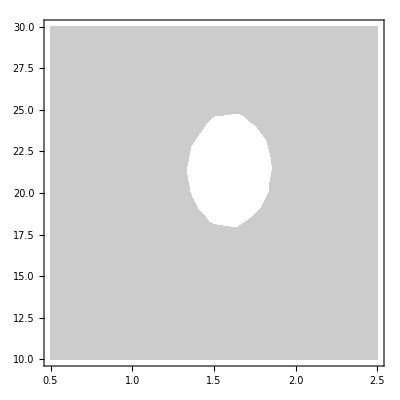

```mathematica
ContourPlot[Exp[-chi2],{cW,0.5,2.5},{cZ,10,30}]
```

```mathematica
{cW,0.5,2.5},{cZ,10,30}
```

```mathematica
Plot3D[Exp[-chi2],{cW,-8,2.5},{cZ,10,100},PlotRange->All]
```

-Graphics3D-

```mathematica
p[x_,y_]:=Exp[-((x-1.1)^2/0.2/0.2+2*0.9*(x-1.1)*(y-1.4)/0.2/0.5+(y-1.4)^2/0.5/0.5)/2]+Exp[-((x-2.1)^2/1.2/1.2+2*0.9*(x-2.1)*(y-1.4)/1.2/0.5+(y-1.4)^2/0.5/0.5)/2];
```

```mathematica
p[x_]:=NIntegrate[p[x,y],{y,-Infinity,Infinity}];
```

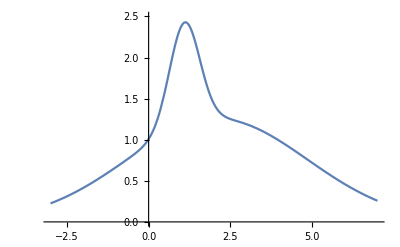

```mathematica
Plot[p[x],{x,-3,7},PlotRange->{{-3,7},{0,2.5}}]
```

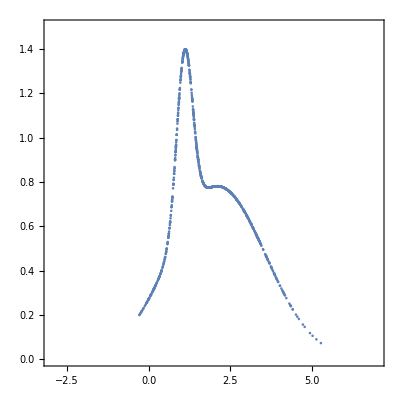

```mathematica
ListPlot[Table[{distMarg[[i,2]],distMarg[[i,1]]},{i,Length[distMarg]}],PlotRange->{{-3,7},{0,1.5}},Frame->True,AspectRatio->1]
```